分母fdと分子fnの定義とその微分fdd,fnd

```mathematica
fd=(4 x^3)/3(Cos[2 d x]+Cosh[2 d x])
fn=Cos[x(d-1)]Sinh[x(d+1)]+Cos[x(1+d)]Sinh[x(1-d)]-Sin[x(d-1)]Cosh[x(1+d)]+Sin[x(1+d)]Cosh[x(1-d)]-2x (Cos[x(d-1)]Cosh[x(1+d)]+Cos[x(1+d)]Cosh[x(1-d)])
fdd=4/3(3 x^2(Cos[2 d x]+Cosh[2 d x])+2 d x^3(-Sin[2 d x]+Sinh[2 d x]))
fnd=-2 d (Sin[x(d-1)]Sinh[x(d+1)]+Sin[x(1+d)]Sinh[x(1-d)])+2x((d-1)Sin[x(d-1)]Cosh[x(1+d)]-(1+d)Cos[x(d-1)]Sinh[x(1+d)]+(1+d)Sin[x(1+d)]Cosh[x(1-d)]-(1-d)Cos[x(1+d)]Sinh[x(1-d)])
```

4/3 x^3 (Cos[2 d x]+Cosh[2 d x])

-2 x (Cos[(1+d) x] Cosh[(1-d) x]+Cos[(-1+d) x] Cosh[(1+d) x])-Cosh[(1+d) x] Sin[(-1+d) x]+Cosh[(1-d) x] Sin[(1+d) x]+Cos[(1+d) x] Sinh[(1-d) x]+Cos[(-1+d) x] Sinh[(1+d) x]

4/3 (3 x^2 (Cos[2 d x]+Cosh[2 d x])+2 d x^3 (-Sin[2 d x]+Sinh[2 d x]))

2 x ((-1+d) Cosh[(1+d) x] Sin[(-1+d) x]+(1+d) Cosh[(1-d) x] Sin[(1+d) x]-(1-d) Cos[(1+d) x] Sinh[(1-d) x]-(1+d) Cos[(-1+d) x] Sinh[(1+d) x])-2 d (Sin[(1+d) x] Sinh[(1-d) x]+Sin[(-1+d) x] Sinh[(1+d) x])

```mathematica
FullSimplify[D[fd,x]==fdd]
```

True

```mathematica
FullSimplify[D[fn,x]==fnd]
```

True

fn*fdd/fd

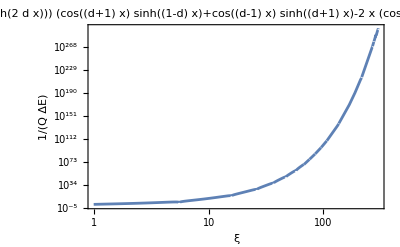

```mathematica
F1=(3/x+2 d (-Sin[2 d x]+Sinh[2 d x])/(Cos[2 d x]+Cosh[2 d x]))*(Cos[x(d-1)]Sinh[x(d+1)]+Cos[x(1+d)]Sinh[x(1-d)]-Sin[x(d-1)]Cosh[x(1+d)]+Sin[x(1+d)]Cosh[x(1-d)]-2x (Cos[x(d-1)]Cosh[x(1+d)]+Cos[x(1+d)]Cosh[x(1-d)]))/.
{d->1.3};
F1g=LogLogPlot[Abs[F1],{x,1,300},PlotLabel->fn*fdd, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

fnd

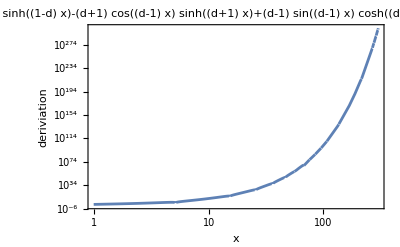

```mathematica
F2=(-2 d (Sin[x(d-1)]Sinh[x(d+1)]+Sin[x(1+d)]Sinh[x(1-d)])+2x((d-1)Sin[x(d-1)]Cosh[x(1+d)]-(1+d)Cos[x(d-1)]Sinh[x(1+d)]+(1+d)Sin[x(1+d)]Cosh[x(1-d)]-(1-d)Cos[x(1+d)]Sinh[x(1-d)]))/.
{d->1.3};
F2g=LogLogPlot[Abs[F2],{x,1,300},PlotLabel->fnd, Frame->True,FrameLabel->{x,deriviation}]
```

cos(d-1)ξ = 0, sin(d-1)ξ = (-1)^n

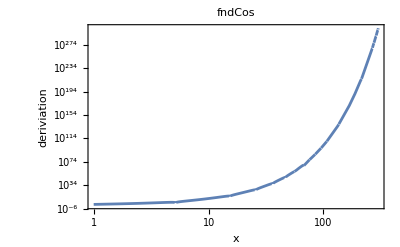

```mathematica
fndC=-2 d (Sin[x(d-1)]Sinh[x(d+1)]+Sin[x(1+d)]Sinh[x(1-d)])+2x((d-1)Sin[x(d-1)]Cosh[x(1+d)]+(1+d)Sin[x(1+d)]Cosh[x(1-d)]-(1-d)Cos[x(1+d)]Sinh[x(1-d)])/.
{d->1.3,x->(2n+1)/(2(d-1)),n->0};
F2g=LogLogPlot[Abs[F2],{x,1,300},PlotLabel->fndCos, Frame->True,FrameLabel->{x,deriviation}]
```